```mathematica
u0=1.*10^-8;α=0.01;a=0.01;V[r_]=-α/r;δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);
Veff[c_,d_][r_]=-α/r Erf[r/(√2 a)]-2π α c a^2 δa[r]+(π α)/2 d a^4(-(3 ⅇ^(-r^2/(2 a^2)))/(2 √2 a^5 π^(3/2))+(ⅇ^(-r^2/(2 a^2)) r^2)/(2 √2 a^7 π^(3/2)));
m=100.;l=0;l1=-1/2+√((l+1/2)^2-(α)^2);
kr:=√((e+m)^2-m^2);knr:=√(2 m e);γ:=(*(√(k^2+m^2) α)/k*)(α m)/k;
er:=√(m^2+k^2);enr:=k^2/(2m);
r2=u0;
r1=50.;
re=1000.;
```

```mathematica
WList={10^-10,10^-8,10^-5,.001,.003,.007,.01,.03,.07,.1,.3,.7,1};
```

```mathematica
Realδ=Module[{EE,(*k,*)Z=1,R,CC,u,f,r0,rule,W,γγ},
Table[
(* Define R(r) *)
W=√(k^2+m^2);
EE=W+m;
(*k=√(EE^2-m^2);*)γγ[k_]:=(√(k^2+m^2) Z α)/k;
R[r_]=r^l1 ⅇ^(-ⅈ k r)Hypergeometric1F1[Chop[l1+1+ⅈ γγ[k]],2l1+2,2ⅈ k r];
CC=(Gamma[2l1+2] ⅇ^(-(π/2)γ))/(Abs@Gamma[l1+1+ⅈ γγ[k]](2k)^(l1+1));
R[r_]=1/CC R[r];
(* Find Subscript[δ, l] *)
u[r_]=r R[r];
f[r_]=Simplify[D[u[r], r]/u[r]];
r0=50;(* Choose Subscript[r, 0] *)
rule=Chop@FindRoot[f[r0]==(k+γγ[k]/r0)Cot[k r0+δ(*+Log[2 k r0]/k*)](*Cot[k r0 -(l1 π)/2+γ Log[2k r0]+δ]*),{δ,0}];
Mod[δ/.rule,π,-π/2]
,{k,WList}]];
```

```mathematica
Realδs[k_]:=Module[{EE,(*k,*)Z=1,R,CC,u,f,r0,rule,W,γ},
(* Define R(r) *)
W=√(k^2+m^2);
EE=W+m;
(*k=√(EE^2-m^2);*)γ=(√(k^2+m^2) Z α)/k;
R[r_]=r^l1 ⅇ^(-ⅈ k r)Hypergeometric1F1[Chop[l1+1+ⅈ γ],2l1+2,2ⅈ k r];
CC=(Gamma[2l1+2] ⅇ^(-(π/2)γ))/(Abs@Gamma[l1+1+ⅈ γ](2k)^(l1+1));
R[r_]=1/CC R[r];
(* Find Subscript[δ, l] *)
u[r_]=r R[r];
f[r_]=Simplify[D[u[r], r]/u[r]];
r0=50;(* Choose Subscript[r, 0] *)
rule=Chop@FindRoot[f[r0]==(k+γ/r0)Cot[k r0+δ(*+Log[2 k r0]/k*)](*Cot[k r0 -(l1 π)/2+γ Log[2k r0]+δ]*),{δ,0}];
Mod[δ/.rule,π,-π/2]
];
```

```mathematica
(*δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];
sol=Flatten@NDSolve[{-u''[x]+2m V u[x]-(en-V)^2/4 u[x]==2m en u[x],u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)(u'[r1] ((en-V)/(8 m)+1)-(f[e,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(e-Veff[c,d][r1])/(8m))f[e,c,d][r1])==(k+γ/r1)  Cot[k r1+δ](*u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
(*PrintTemporary["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]*)
```

```mathematica
sol1=ParametricNDSolve[{-f''[x]+2m Veff[c,d][x]f[x]-(enr-Veff[c,d][x])^2/4 f[x]==2m enr f[x],f'[r2]==1,f[r2]==u0},f,{x,r1,r2},{k,c,d},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50]
```

{f→ParametricFunction[<>]}

```mathematica
Block[{mon,temp1,temp2},Monitor[FindRoot[{Block[{k=10^-10},(temp1=((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[1]]])/.sol1)==0],Block[{k=10^-5},(temp2=((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[2]]])/.sol1)==0]}(*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*),{{c,1,1.5},{d,0,1}},MaxIterations->10000,AccuracyGoal->8,WorkingPrecision->30,StepMonitor:>{mon={N[{c,d},10],{temp1,temp2}};If[Abs[temp1]<10^-5&&Abs[temp2]<10^-5,Print@mon]}],mon]]
```

FindRoot::precw: 参数函数的精度 ({-0.499393+((1+Times[«2»]) ParametricFunction[«6»][«3»]'[50.]-0.00125 (4.×10^-6+Times[«2»]+Times[«2»]) ParametricFunction[1,Internal`Bag[<1>],1,1,{«6»},{«2»}][1/10000000000,c,d][50.])/((1+0.00125 Plus[«3»])«1»ParametricFunction[1,Internal`Bag[<1>],1,1,{{«3»},System`Utilities`HashTable[<4>],«2»,{«3»},{«3»}},{NDSolve`base$2376,NDSolve`NDSolveParametricFunction[«10»]}][«1»]«1»«4»])==0,-«20»+(«1»)/(«1»)==0}) 小于 WorkingPrecision (30.).

{{1.42421,-7.80067},{3.37127×10^-6,3.39172×10^-6}}

{{1.40409,-3.33591},{3.08553×10^-6,3.10599×10^-6}}

{{1.39352,-1.02625},{-1.03088×10^-6,-1.01047×10^-6}}

{{1.393523586,-1.026246034},{-1.03028×10^-6,-1.00983×10^-6}}

{{1.396876848,-1.759285032},{5.81762×10^-7,6.02647×10^-7}}

{{1.396876848,-1.759284967},{5.81461×10^-7,6.01779×10^-7}}

{{1.39568963,-1.499753519},{4.30622×10^-8,6.36717×10^-8}}

{{1.395618853,-1.484281279},{9.97752×10^-9,3.04323×10^-8}}

{{1.395854916,-1.535885939},{1.20355×10^-7,1.40809×10^-7}}

{{1.395594997,-1.479067314},{-1.35028×10^-9,1.91046×10^-8}}

{{1.395577207,-1.475125921},{-8.96355×10^-9,1.14922×10^-8}}

{{1.439843691,-12.4937264},{-2.69222×10^-6,-2.67177×10^-6}}

FindRoot::cvmit: 无法在 10000 次迭代中收敛到要求的准确度或者精度.

{c→1.53236557445387917999919478953,d→-31.7815457275043785629786251877}

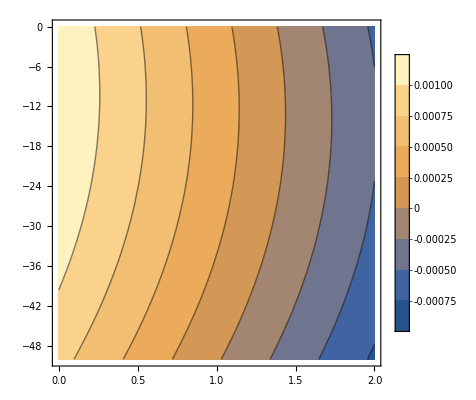

```mathematica
ContourPlot[Block[{k=10^-10},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[1]]])/.sol1)],{c,0,2},{d,0,-50},PlotLegends->Automatic]
```

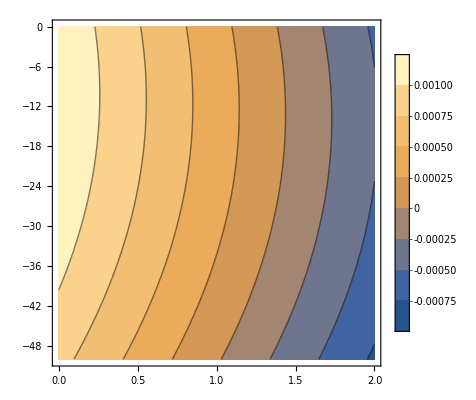

```mathematica
ContourPlot[Block[{k=10^-5},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[2]]])/.sol1)],{c,0,2},{d,0,-50},PlotLegends->Automatic]
```

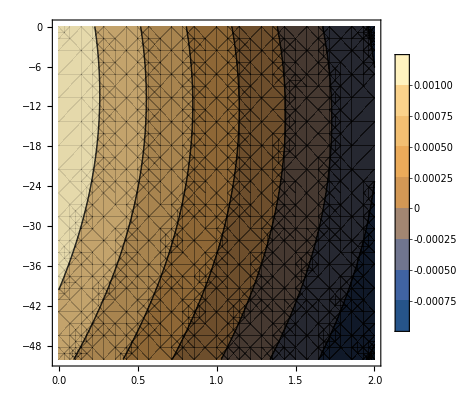

```mathematica
Show[ContourPlot[Block[{k=10^-10},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[1]]])/.sol1)],{c,0,2},{d,0,-50},PlotLegends->Automatic,ContourStyle->None],ContourPlot[Block[{k=10^-5},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[2]]])/.sol1)],{c,0,2},{d,0,-50},PlotLegends->Automatic,PlotTheme->"Monochrome"]]
```

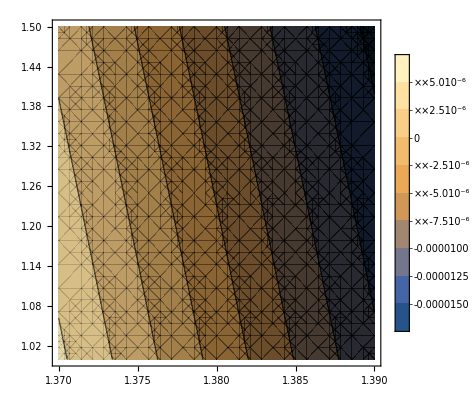

```mathematica
Show[ContourPlot[Block[{k=10^-10},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[1]]])/.sol1)],{c,1.37,1.39},{d,1,1.5},PlotLegends->Automatic,ContourStyle->None],ContourPlot[Block[{k=10^-5},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[2]]])/.sol1)],{c,1.37,1.39},{d,1,1.5},PlotLegends->Automatic,PlotTheme->"Monochrome"]]
```

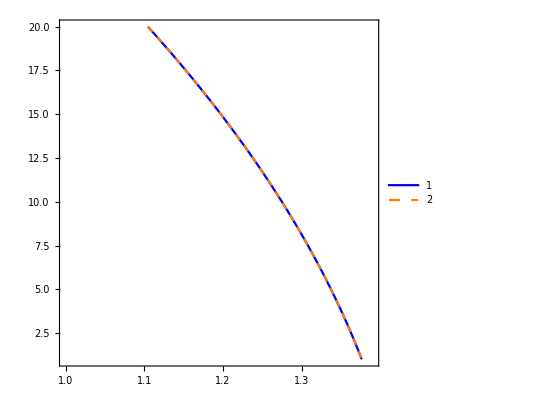

```mathematica
ContourPlot[{Block[{k=10^-10},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[1]]])/.sol1)],Block[{k=10^-8},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[2]]])/.sol1)]},{c,1.,1.39},{d,1,20},PlotLegends->Automatic,ContourStyle->{Blue,{Orange,Dashed}}]
```

```mathematica
Block[{c=1.375,d=1.12},{Block[{k=10^-10},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[1]]])/.sol1)],Block[{k=10^-5},(((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-(k+γ/r1)  Cot[k r1+Realδ[[2]]])/.sol1)]}]
```

{1.88015×10^-7,2.0847×10^-7}

```mathematica
(*with no 2πα coefficients*)
```

```mathematica
{c,d}={-9.413438491692380419`10.,-0.27105515682638172060954793531699638608`10.};
```

```mathematica
{c,d}={5.0754843991730544455`10.,-30.677980928125758848`10.};
```

```mathematica
(*with coefficients*)
```

```mathematica
{1.17593586050124084237864928710020534586`10.,-42.6358404717032391282`10.};
```

```mathematica
{1.39559499652371611822027335911510989238`10.,-1.47906731384361825540418538527863749097`10.};
```

```mathematica
Block[{mon,temp1,temp2,n=0,δ1,δ2},Monitor[FindRoot[Thread[({temp1,temp2}=Table[(f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-((k+γ/r1)  Cot[k r1+(Evaluate[ToExpression["δ"<>Switch[k,10^-10,"1",10^-5,"2"]]]=Realδs[k])])/.sol1,{k,{10^-10,10^-5}}])=={0,0}]
(*Cot[k r1 -(l1 π)/2+γ Log[2k r1]+Realva[[1]]]*),{{c,-1,-2},{d,1,2}},MaxIterations->10000,AccuracyGoal->8,WorkingPrecision->30,StepMonitor:>{n++;mon={N[{c,d},10],{temp1,temp2},n};If[Abs[temp1]<10^-5&&Abs[temp2]<10^-5,Print@mon]}],mon]]
```

FindRoot::precw: 参数函数的精度 ({-0.499393+((1+Times[«2»]) ParametricFunction[«6»][«3»]'[50.]-0.00125 (4.×10^-6+Times[«2»]+Times[«2»]) ParametricFunction[1,Internal`Bag[<1>],1,1,{«6»},{«2»}][1/10000000000,c,d][50.])/((1+0.00125 Plus[«3»])«1»ParametricFunction[1,Internal`Bag[<1>],1,1,{{«3»},System`Utilities`HashTable[<4>],«2»,{«3»},{«3»}},{NDSolve`base$1794,NDSolve`NDSolveParametricFunction[«10»]}][«1»]«1»«4»])==0,-«20»+(«1»)/(«1»)==0}) 小于 WorkingPrecision (30.).

$Aborted

```mathematica
Block[{c=-21,d=-31},Table[((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])/.sol1)-((k+γ/r1)  Cot[k r1+(Evaluate[ToExpression["δ"<>Switch[k,10^-10,"1",10^-5,"2"]]])]),{k,{10^-10,10^-5}}]]
```

{1.74715,1.74715}

```mathematica
Block[{c=-21,d=-31,k=10^-10},((f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])/.sol1)-(k+(Print[γ];γ)/r1)  Cot[k r1+δ1]]
```

1.×10^10

1.74715

```mathematica
Block[{c=5,d=-30},Table[(f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])-((k+γ/r1)  Cot[k r1+(Evaluate[ToExpression["δ"<>Switch[k,10^-10,"1",10^-5,"2"]]]=Realδs[k])])/.sol1,{k,{10^-10,10^-5}}]]
```

Set::setraw: 无法赋值给原始对象 1.5708.

Set::setraw: 无法赋值给原始对象 1.57005.

{0.0358287,-0.463559}

```mathematica
Block[{c=5,d=-30},Table[(f[k,c,d]'[r1] ((k-Veff[c,d][r1])/(8 m)+1)-(f[k,c,d][r1] Veff[c,d]'[r1])/(8 m))/((1+(k-Veff[c,d][r1])/(8m))f[k,c,d][r1])/.sol1,{k,{10^-10,10^-5}}]]
```

{0.0358337,0.0358337}

```mathematica
Block[{c=5,d=-30},Table[((k+γ/r1)  Cot[k r1+Realδs[k]]),{k,{10^-10,10^-5}}]]
```

{4.99393×10^-6,0.499393}

```mathematica
Clear[δ1,δ2]
```

```mathematica
δ1
```

1.5708

```mathematica
(*hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[10^-9,c2,d1]-δexpminus9,8];*)
```

```mathematica
(*Determinec2d1[{c2start_,c2end___},{d1start_,d1end___}]:=Module[{findroot,mon},
Monitor[findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[10^-9,c2,d1]==δexpminus9},{{c2,c2start,c2end},{d1,d1start,d1end}},MaxIterations->100,AccuracyGoal->20,PrecisionGoal->20,WorkingPrecision->50,StepMonitor:>{mon={c2,d1,evnhhh1,evnhhh2};If[evnhhh1<10^-7&&evnhhh2<10^-7,Print@mon]}],mon];
{c2,d1}/.findroot
]*)
```